```mathematica
(*We look here to show a discrete plot of our situation*)
```

```mathematica
(*We also generate our specific distances*)
num=2^15;
range=20;(*Distance in fm*)
δx=range/num//N;
δk=(2π)/(num δx)//N;
```

```mathematica
space=Table[(j-(num/2))*δx+10,{j,1,num}];
kspace=Table[(j-(num/2))*δk,{j,1,num}];
absk=Table[kspace[[j]]+k0,{j,1,num}];
```

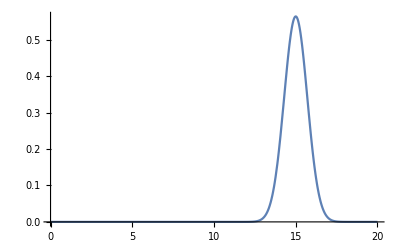

```mathematica
(*First we define our original basic stationary gaussian*)(*All in fm*)
μ=5;
a=7;
V0=50;(*MeV*)
x0=15;
σ0=1;
k0=1/15;
n=(1/π)^(1/4);(*Only the case for the above conditions*)
x=.;
ψ[x_]:=n Exp[-((x-x0)^2)/(2σ0^2)]*Exp[-I k0 x];

Plot[ψ[x]*Conjugate[ψ[x]],{x,0,20},PlotRange->All]
```

```mathematica
(*Now here we set up as our arrays of data that we are going to make into our FFT*)
exdata=Table[ψ[space[[j]]],{j,1,num}];
nydata=RotateLeft[exdata,num/ 2−1];
ekdata=Chop[RotateRight[Fourier[nydata],num / 2−1]];
Ikdata=ekdata Conjugate[ekdata];
Ikdata[[4000]]
```

6.92979×10^-17+0. ⅈ

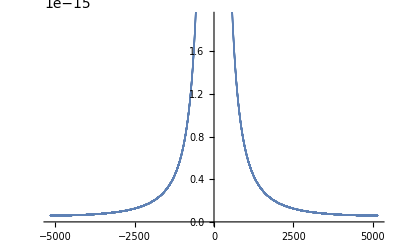

```mathematica
ListPlot[Table[{kspace[[j]],Ikdata[[j]]},{j,1,num}]]
```

```mathematica
(*Now we inverse fourier transform back to get our original wavefunction*)
nydata=RotateLeft[ekdata,num/2-1];
ex2data=Chop[RotateRight[InverseFourier[nydata],num/2-1]];
Ix2data=ex2data Conjugate[ex2data];
```

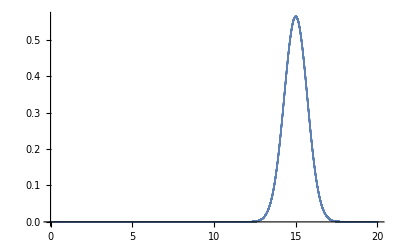

```mathematica
(*So now we have our discretized wavefunction for the situation*)
ListPlot[Table[{space[[j]],Ix2data[[j]]},{j,1,num}],PlotRange->All]
```

```mathematica
(*Now we look to time evolve our Gaussian using the Chebyshev propagator*)
(*To do this we first have to put the situation onto the grid*)
(*We can now normalize our wavefunction over all space, because whenever we would put in a time dependence this would fall out over the integral.  Here we will normalize by summing.*)
```

```mathematica
x=.;
t=.;
NDSolve[{I hbar D[Ψ[x,t],t]==-hbar^2/(2μ)D[D[Ψ[x,t],x],x],Ψ[x,0]==ψ[x]},Ψ[x,t],{x,0,20},{t,0,5}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{ⅈ hbar Ψ^(0,1)[x,t]==-1/10 hbar^2 Ψ^(2,0)[x,t],Ψ[x,0]==(ⅇ^(-1/2 (-15+x)^2-(ⅈ x)/15))/π^(1/4)},Ψ[x,t],{x,0,20},{t,0,5}]

```mathematica
(*This generates the Kinetic energy values in our system*)
Tfunction[x_]=D[D[ψ[x],x],x];
Tvalues=Table[Tfunction[j],{j,1,num}];
```

```mathematica
(*In order to fast fourier transform the recipe says that we must take psi to momentum space, then multiply it by T and then fourier transform back into real space.*)
Tekdata=Table[ekdata[[j]]*hbar^2 j^2/(2μ),{j,1,num}]
```

```mathematica
(*The next step is then to back transform this into real space.*)
nyTdata=RotateLeft[Tekdata,num/2-1];
Tex2data=Chop[RotateRight[InverseFourier[nyTdata],num/2-1]];
TIx2data=Tex2data Conjugate[Tex2data];
ListPlot[Table[{space[[j]],TIx2data[[j]]},{j,1,num}]]
```

InverseFourier::fftl: Argument {(2.46609×10^8-3.84071×10^8 ⅈ) hbar^2,(3.73361×10^8+2.39732×10^8 ⅈ) hbar^2,«7»,(8.52702×10^6+5.475×10^6 ⅈ) hbar^2,«32758»} is not a non-empty list or rectangular array of numeric quantities.

Part::partw: Part 3 of Conjugate[InverseFourier[{(2.46609×10^8-3.84071×10^8 ⅈ) hbar^2,(3.73361×10^8+2.39732×10^8 ⅈ) hbar^2,«8»,«32758»}]] InverseFourier[{«1»}] does not exist.

Part::partw: Part 4 of Conjugate[InverseFourier[{(2.46609×10^8-3.84071×10^8 ⅈ) hbar^2,(3.73361×10^8+2.39732×10^8 ⅈ) hbar^2,«8»,«32758»}]] InverseFourier[{«1»}] does not exist.

Part::partw: Part 5 of Conjugate[InverseFourier[{(2.46609×10^8-3.84071×10^8 ⅈ) hbar^2,(3.73361×10^8+2.39732×10^8 ⅈ) hbar^2,«8»,«32758»}]] InverseFourier[{«1»}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
(*We also must find the potential energy of our system in some way. Since it is local in space all we have to do is multiply it directly agains our value of ψ in order to get this value.*)
x=.;
V[x_]:=Piecewise[{{0,x<10},{-V0,0<=x<=a},{0,x>a}}]
Vvalues=Table[V[j]ψ[j],{j,1,num}];
```

```mathematica
(*Now that we have both the Kinetic and potential energy, we just look to time evolve each of them together and then reiterate and repeat the process again.*)
(*The process goes like this.  Find T and V for the system, time evolve one step, then with the new wavefunction find T and V again and keep progressing this through each time step.*)

(*Logically I think the next step is to store the next time step in the next line of the vector that we have for our Kinetic energy and Potential energy matrices.  Then we just take values from each of these to generate the next step of our psi.  

By the end we look to have a matrix representation for our ψ that in each column generates a new time step in our situation.

The next step here is to use the chebyshev propagator in order to advance time by one step and then fill in the other matrices back in until everything is filled out correctly.*)
```

```mathematica
Hnorm=2(H-IdentityMatrix[num]((Max[Tex2data]+Max[Vvalues]-Min[Vvalues])/2+Min[Vvalues])/(Max[Tex2data]+Max[Vvalues]-Min[Vvalues]))
```

Max::nord: Invalid comparison with -35.1443+4.37543 ⅈ attempted.

Max::nord: Invalid comparison with -11.6832-92.9923 ⅈ attempted.

Max::nord: Invalid comparison with -9.2283-1.09696 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

$Aborted

```mathematica
x=.;
dt=.01;
delta= .01;
J=Length[space]-1;
dx=space[[2]]-space[[1]];
Hmax=0+1/dx^2;
τ=Hmax dt;
ii=2;
Jnτ={BesselJ[0,τ],-2x BesselJ[1,τ]};
While[True, 
tmp=2 (-1 x)^ii BesselJ[ii,τ]
If[Abs[tmp/(x^ii)]<delta,
Break[]]
Append[Jnτ,tmp]
ii+=1];
Npoly=Length[Jnτ]
```

Part::partd: Part specification space⟦2⟧ is longer than depth of object.

Part::partd: Part specification space⟦1⟧ is longer than depth of object.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

2

-0.00532262 x^2